```mathematica
(*Task #1*)
f[M_,u_]:=4 π n (M/(2π R T))^(3/2)ⅇ^(-M/(2 R T)u^2)u^2
(*n：分子数密度，即单位体积内的气体分子数目；M：气体分子的摩尔质量；麦克斯韦速度分布律：单位体积内，速度介于 u~u+du 的气体分子数目；*)
```

```mathematica
ρ[M_,u_]:=4 π(M/(2π R T))^(3/2)ⅇ^(-M/(2 R T)u^2)u^2
(*是否应该用rho替代f ？！*)
```

```mathematica
rule={R->8.31,T->500};
```

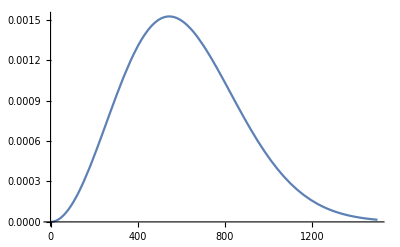

```mathematica
Plot[ρ[0.028,u]/.rule,{u,0,1500}]
(*使用规则变换，避免与后续的符号计算冲突。*)
```

```mathematica
Integrate[ρ[M,u],{u,0,Infinity},Assumptions->M/(R T)>0]
(*为了检验是否定义正确，可以进行积分；为了避免返回条件表达式，使用Assumptions选项！*)
```

1

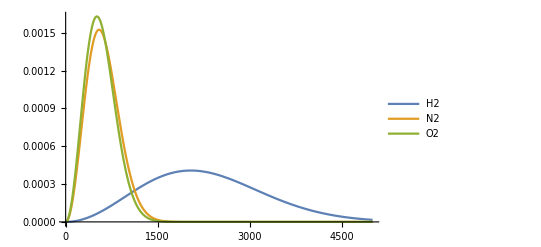

```mathematica
Plot[{ρ[0.002,u]/.rule,ρ[0.028,u]/.rule,ρ[0.032,u]/.rule},{u,0,5000},PlotRange->All,PlotLegends->{"H2","N2","O2"}]
```

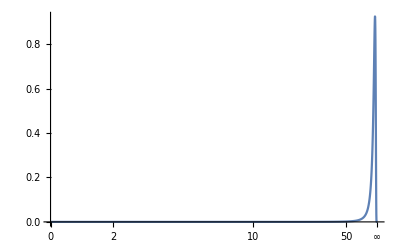

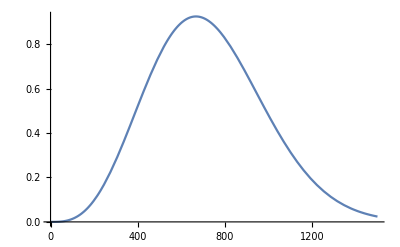

```mathematica
(*Task #2 平均速率（权重平均值 uwa） 针对上述三种气体*)Plot[u ρ[0.028,u]/.rule,{u,0,Infinity},PlotRange->All]
Plot[u ρ[0.028,u]/.rule,{u,0,1500},PlotRange->All]
```

```mathematica
Integrate[u ρ[M,u],{u,0,Infinity},Assumptions->M/(R T)>0]
```

2 √(2/π) √((R T)/M)

```mathematica
uwa[M_]:=Sqrt[(8R T)/(π M)]
```

```mathematica
uwa[0.002]/.rule
```

2300.07

```mathematica
uwa[0.028]/.rule
```

614.719

```mathematica
uwa[0.032]/.rule
```

575.017

```mathematica
{uwa[0.002],uwa[0.028],uwa[0.032]}/.rule
(*利用“列表”简化。*)
```

{2300.07,614.719,575.017}

```mathematica
(*Task #3 最概然速率 巩固符号计算！*)Plot[{ρ[0.002,u]/.rule,ρ[0.028,u]/.rule,ρ[0.032,u]/.rule},
{u,0,5000},PlotRange->All,PlotLegends->{"H2","N2","O2"}]
```

-Graphics-

```mathematica
Solve[D[ρ[M,u],u]==0,u]
```

{{u→0},{u→-(√2 √R √T)/(√M)},{u→(√2 √R √T)/(√M)}}

```mathematica
ump[M_]:=Sqrt[2 R T/M]
```

```mathematica
{ump[0.002],ump[0.028],ump[0.032]}/.rule
```

{2038.38,544.78,509.595}

```mathematica
Maximize[{ρ[M,u]/.rule/.{M->0.002},u>0&&u<5000},u]
```

{0.000407291,{u→2038.38}}

```mathematica
Maximize[{ρ[M,u]/.rule/.{M->0.028},u>0&&u<5000},u]
```

{0.00152394,{u→544.78}}

```mathematica
Maximize[{ρ[M,u]/.rule/.{M->0.032},u>0&&u<5000},u]
```

{0.00162916,{u→509.595}}